Natural mortality rate from Hoenig (1983), reported in Bishop_2004

```mathematica
mortalityrate = Exp[1.46 - 1.01*(Log[tmax])]
```

4.30596/tmax^1.01

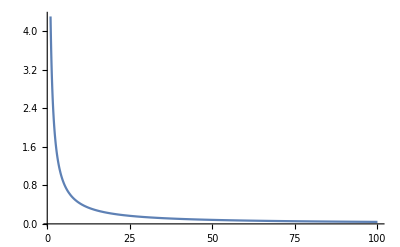

```mathematica
Plot[mortalityrate,{tmax,1,100},PlotRange->{0,All}]
```

Mortality rate for a shark that lives 33 years (max from our model)

```mathematica
mortalityratesec=(mortalityrate/.tmax->33)/(365*24*60*60)
```

3.99544×10^-9

This compares well with our current rate of 3.076*10^-9... from: 
Sand tiger shark mortality: Z = 0.18 to 0.097 yr-1

```mathematica
0.097/(60*60*24*365)
0.18/(60*60*24*365)
```

3.07585×10^-9

5.70776×10^-9

From Robbins (Current Biology) 2006:
Type III survivorship curve for reef sharks
i= age c1,c2,c3 are fitted parameters

```mathematica
logsurvshp = c1/(1+(c2-1)*Exp[-c3*i])
```

c1/(1+(-1+c2) ⅇ^(-c3 i))

Age-specific instantaneous mortality rates of C. amblyrhynchos were then obtained by differentiating the curve at each age.

```mathematica
D[logsurvshp,i]
```

(c1 (-1+c2) c3 ⅇ^(-c3 i))/((1+(-1+c2) ⅇ^(-c3 i))^2)

BUT - the ASSHOLES don’t give the parameterizations.

From Cortes 1998: “Survivorship  for  all  large  coastal  sharks  (lemon, sandbar, dusky, and blacktip sharks) over
 100 cm TL was assumed to be constant for all age groups, considering  that  after  they  reach  that  size predation  on these   species   is   probably   minimal”
 
 So perhaps it is better to have a constant mortality rate...

REPRODUCTION

Cortes: “Conversely, the estimates of population growth may have been too liberal, based on the fertility schedules
used. As in other demographic analyses (Cortes and Parsons, 1996) I assumed that all mature females are
reproductively active every breeding season and that older females do not exhibit reproductive senescence. Indeed,  no  decreases  in  reproductive  rates  at  older ages have been documented in sharks”

Cortes 1996: “4.45 and 4.65 female pups/female in Tampa Bay and Florida Bay, respectively” for Bonnetthead sharks

```mathematica
fecundity = 4.65/(60*60*24*365)
N[(1/2)/(60*60*24*365)]
```

1.47451×10^-7

1.58549×10^-8

MIGRATION

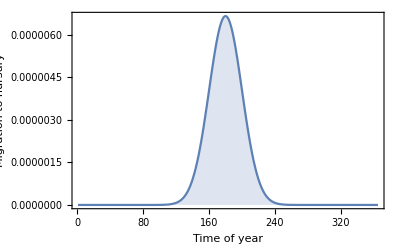

```mathematica
migrationrate = DD*(velocity/distance)*Exp[(-(day-peakday)^2)/(2*tau^2)];Plot[migrationrate/.{DD->10,velocity->1,distance->1500*1000,peakday->180,tau->20},{day,1,365},PlotRange->{0,All},Frame->True,FrameLabel->{"Time of year","Migration to nursury"},Filling->Bottom]
```

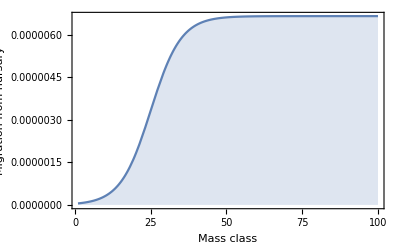

```mathematica
juvmigrationrate = DD*(velocity/distance)/(1 + Exp[-(1/sigtau)*(mass-massjuv)]);
Plot[juvmigrationrate/.{DD->10,velocity->1,distance->1500*1000,massjuv->25,sigtau->5},{mass,1,100},PlotRange->{0,All},Frame->True,FrameLabel->{"Mass class","Migration from nursury"},Filling->Bottom]
```

Tooth length conversion
Shimada: bodylength (cm) = -26.665+12.499*crownheight (mm)

```mathematica
Remove[BLcm]
```

```mathematica
Solve[BLcm == -26.665+12.499*CHmm,CHmm]
```

{{CHmm→-0.0800064 (-26.665-BLcm)}}

```mathematica
Reduce[MASSg == (0.00013*BLcm^2.4)*1000,BLcm];
```

Reduce::ratnz: Reduce was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

Reduce::useq: The answer found by Reduce contains unsolved equation(s) {0==-(1.18533 (-1. («1»)^(36«1»«1»)+«1»))/MASSg^(35/12),0==(«1»)/(«5»)^(«1»),«7»,0==-(«1»)/(«1»),0==-((«1») («1»))/MASSg^(35/12)}. A likely reason for this is that the solution set depends on branch cuts of Wolfram Language functions.

```mathematica
ToothLength=-0.08000640051204096 (-26.665-(Exp[(1/2.4)*Log[Massg/(1000*0.00013)]]))
```

-0.0800064 (-26.665-2.33986 Massg^0.416667)

```mathematica
FullSimplify[ToothLength]
```

2.13337+0.187204 Massg^0.416667